# Ejercicio : PushDown Automata

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Código

Definimos la función POP

```mathematica
SetAttributes[Pop,HoldAll]
Pop[string_]:=Check[{StringTake[string,1],Check[string=StringDrop[string,1],string=""]},{"",""}]
```

Definimos la función PUSH

```mathematica
Push[string_,a_]:=StringInsert[string,a,1]
```

Hay que notar que el push retorna un string con el push aplicado, pero no modifica el original

## Primero probaremos con un automata sencillo

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

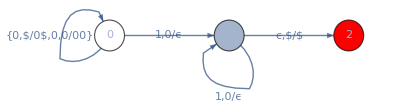

```mathematica
ShowGraphFA[{0->0,0->1,1 ->1,1->2},{0,1,2},{0},{2},{"{0,$/0$,0,0/00}","1,0/ϵ","1,0/ϵ","ϵ,$/$"}]
```

Definimos la asociación

```mathematica
δ= Association[
{0,"0","$"}->{0,"0$"},
{0,"0","0"}->{0,"00"},
{0,"1","0"}->{1,""},
{1,"1","0"}->{1,""},
{1,"","$"}->{2,"$"}
];
```

Definimos la función DeltHat

```mathematica
DeltaHat[{state_,string_,stack_}]:=Block[{trans, tempstack=stack,tempstring=string},
trans=δ[{state,First[Pop[tempstring]],First[Pop[tempstack]]}];
{First[trans],tempstring,Push[tempstack,Last[trans]]}
]
```

Debemos crear una función que nos de bajo la configuración que tenemos a cuales estados podemos llegar por medio de las transiciones EPSILON, a esta le llamaremos Closure

```mathematica
Closure[currentState_, currentString_, currentStack_] := First[δ[{currentState,"",currentStack}]];
```

Ahora debemos crear una función que nos de las transiciones desde un estado hacia su clausura pero respetando los valores del STRING y STACK que tiene antes de aplicar el DeltaHat sobre el estado, ademas debemos aplicar esta lógica solo si es posible, si no agregamos Nothing al camino de transiciones.

```mathematica
DeltaHatWithEpsilonClosure[{state_,string_,stack_}] := Block[{epsilonNextState,tempstack=stack,tempstring=string},
epsilonNextState=Closure[state,tempstring,StringTake[tempstack,1]];
{Check[DeltaHat[{state,string,stack}],Nothing],If[NumericQ[epsilonNextState],Check[DeltaHat[{epsilonNextState, tempstring, tempstack}],{epsilonNextState,tempstring,tempstack}], Nothing]}
];
```

Ahora creamos una función recursiva que nos de el árbol de {estado,string,stack} que genera el automata de pila con el string dado, funciona de la siguiente manera : Tomamos de raíz el estado inicial, la configuración de stack y el string, a partir de este aplicamos DeltaHatWithEpsilonClosure y lo guardamos en “tree” recursivamente hasta que encontramos un “{}” debido a que no existe forma de generar mas transiciones, o nos encontramos con un nivel de arbol totalmente igual a uno ya insertado en el arbol (Quiere decir que llegamos a las hojas)

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[initialState_, expression_,stack_]:=
Block[{},
root={initialState, expression,stack};
tree ={};
firstLevel =  DeltaHatWithEpsilonClosure[root];
(* Aplicamos recursivamente, DeltaHatWithEpsilonClosure hasta que no se pueda mas y paramos cuando encontramos un vacio o el nivel de hojas se repite*)
NestWhileList[Last[AppendTo[tree, Flatten[Table[DeltaHatWithEpsilonClosure[i],{i,#}],1]]] /. # -> {}&,firstLevel,# != {}  &];
{root,firstLevel /. {} -> Nothing, tree /. {} -> Nothing}
];
```

Primero probamos con el ejemplo mas sencillo el string “01”

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[0,"01","$"]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringInsert::string: String expected at position 2 in StringInsert[,{2,,$},1].

StringTake::take: Cannot take positions 1 through 1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringInsert::string: String expected at position 2 in StringInsert[,{2,,$},1].

{{0,01,$},{{0,1,0$}},{{{1,,$}},{{2,,$}}}}

Como podemos ver llegamos al estado  q2, y el árbol fue generado correctamente

Probamos con el string “0011”

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[0,"0011","$"]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringInsert::string: String expected at position 2 in StringInsert[,{2,,$},1].

StringTake::take: Cannot take positions 1 through 1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

StringInsert::string: String expected at position 2 in StringInsert[,{2,,$},1].

{{0,0011,$},{{0,011,0$}},{{{0,11,00$}},{{1,1,0$}},{{1,,$}},{{2,,$}}}}

Como podemos ver llegamos al estado  q2, y el árbol fue generado correctamente

Ahora lo probamos con un ejemplo que no es valido

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[0,"00011","$"]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringInsert::string: String expected at position 2 in StringInsert[$,{1,,0},1].

{{0,00011,$},{{0,0011,0$}},{{{0,011,00$}},{{0,11,000$}},{{1,1,00$}},{{1,,0$}}}}

## Ejemplo figura 6.2

Veamos el ejemplo del palindrome

```mathematica
δ= Association[
{0,"0","$"}->{0,"0$"},
{0,"1","$"}->{0,"1$"},
{0,"0","0"}->{0,"00"},
{0,"0","1"}->{0,"01"},
{0,"1","0"}->{0,"10"},
{0,"1","1"}->{0,"11"},
{0,"","$"}->{1,"$"},
{0,"","0"}->{1,"0"},
{0,"","1"}->{1,"1"},
{1,"0","0"}->{1,""},
{1,"1","1"}->{1,""},
{1,"","$"}->{2,"$"},
{2,"","$"}->{2,"$"}
];
```

## Lo probamos con un palindrome

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[ 0,"1111","$"]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

StringInsert::string: String expected at position 2 in StringInsert[,{2,1,$},1].

General::stop: Further output of StringInsert::string will be suppressed during this calculation.

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

{{0,1111,$},{{0,111,1$},{1,1111,$}},{{{0,11,11$},{1,11,$},{2,1111,$}},{{0,1,111$},{1,1,1$},{2,11,$},{2,1111,$}},{{0,,1111$},{1,,11$},{1,,$},{2,11,$},{2,1111,$}},{{1,,1111$},{2,,$},{2,11,$},{2,1111,$}},{{2,,$},{2,11,$},{2,1111,$}},{{2,,$},{2,11,$},{2,1111,$}}}}

Como podemos ver se llegó a q2 con la pila y el string vació y se generó todo este arbol, por niveles.

## Ahora lo probamos con un NO palindrome

```mathematica
iterateDeltaHatWithEpsilonClosuresTranstions[ 0,"110","$"]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

StringInsert::string: String expected at position 2 in StringInsert[,{2,1,$},1].

General::stop: Further output of StringInsert::string will be suppressed during this calculation.

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringTake::take: Cannot take positions 1 through 1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

General::stop: Further output of StringDrop::drop will be suppressed during this calculation.

{{0,110,$},{{0,10,1$},{1,110,$}},{{{0,0,11$},{1,0,$},{2,110,$}},{{0,,011$},{1,0,11$},{2,0,$},{2,110,$}},{{1,,011$},{2,0,$},{2,110,$}},{{2,0,$},{2,110,$}},{{2,0,$},{2,110,$}}}}

Como podemos observar se llegó a q2 pero nunca con el string y la pila vacía